## 3.029 Spring 2022 Lecture 05 - 02/14/2022

## Thermodynamic Quantities

We will assume you have heard about fundamental quanties

Internal Energy,

Entropy,

Temperature, T

Forces against which work is done, such as Pressure P.

The combined form of the first and second law is written in terms of these quantities.

Or, we may consider that:

the first law implies the existence of the internal energy U along with its conservation.
the second law implies the existence of the entropy  S  along with its property that it is maximized at equilibrium.

From these quantities, other quantities can be derived (but they are not independent)

Enthalpy,

Helmholtz Free Energy,   (note: some books use the symbol )

Gibbs Free Energy,

Let’s see how these thermodynamic potentials appear in the physics of  the Van der Waals gas

## Phenomenological Thermodynamics

A thermodynamic system is completely characterized by the following thermodynamic variables:

Extensive

Mole number of component ,

Volume,

Entropy,

Internal Energy,

Intensive

Chemical potential of component ,

Pressure,

Temperature,

Note. Some refer to ratios of extensive quantities such as mass/volume or volume/n_j.  It is better to call these quantities densities (e.g., “the mass density” or “the molar volume”), and reserve intensive variables as “the quantities against which changes in extensive variables do work (i.e., forces)”

In the second expression, the full dependencies of the free energies and the system’s state functions are made explicit.

In the dU, the last two terms represent the reversible volumetric (-PdV) and chemical (μ_j dn_j) work that can performed to change the internal energy.   If there are other types of work that can be applied (e.g.,  ), those must be added as well. 
TdS is the reversible heat.

A subtle note is that the 2 + m variables must be independent.  In an ideal gas, the addition of a single species  must change the volume via its partial molar volume. So, they are not independent:  is usually left off in the case of an ideal gas.  However, it can be put back in via the partial pressures and partial molar volumes—in which case PdV  is replaced with  and this effectively plays the role of the chemical potentials.

One way to think of the U  is a surface embedded in   space.  The shape of the surface depends on material properties.
The gradient of U  is:



and the directional derivative along a particular path on the surface U is

 
 
 Where the path is a curve  embedded in the surface U.

If a particular path is considered, say , then the change in U along that path is:


where, suppose an experimentalist adds a bit of heat, volume, number of species, etc, as a function of time.
In other words  is a process.

The combination of the first and and second laws of thermodynamics implies that (at equilibrium):

If heat can flow between any pair of subsystems, T must be uniform and constant.

If volume can be exchange between  any pair of subsystems, P must be uniform and constant.

If a chemical species j can be exchange between any pair of subsystems, μ_j must be uniform and constant.

Because U is a function of extensive variables only (G,F,and H do not have this property), if we take any two subsystems in equilibrium then

because the intensive variables are equal because the systems are in equilibrium.

Therefore we can add up a bunch of little systems to make a system of arbitrary size:

This process is call Euler Integration and it applies to all functions that have this property:  which is called function that is homogeneous-degree-1.

However, we can also take a total differential of the Euler equality

Setting the two definitions equal to each other, we obtain constraints on the intensive variables

This is known as the Gibbs-Duhem relation.  It says that we cannot  change all of the intensive variables arbitrarily and maintain equilibrium.

### Thermodynamic Potentials

Depending on the experimental conditions we’re interested in, we can re-cast the fundamental thermodynamic relation in more natural variables.

Starting with the internal energy

its natural variables are:

Entropy,

Volume,

Mole numbers,

We can easily re-arrange this for entropy

with natural variables:

Internal Energy, U

Volume,

Mole numbers,

To get the other thermodynamic potentials, like Helmholtz and Gibbs Free Energies, we need to do a bit more work

Rigorously, the transformation we’ll use is called a Legendre Transform and we’ll talk more about it next lecture 
(I promise you have seen this in at-least two different contexts so far in your studies!)

We will sketch out the procedure today:

If we want to transform the internal energy such that a new intensive variable  is a natural variable, we start by defining a new potential as the difference of the internal energy with the product of this intensive variable and its extensive conjugate

We then take the total differential of our new thermodynamic potential

And finally, use the fundamental thermodynamic relation to substitute for  and simplify our expression

#### Examples

Let’s say we wanted to express the thermodynamic potential with Temperature as a natural variable (whose extensive conjugate is Entropy)

This thermodynamic is called the Helmholtz Free Energy with natural variables:

Temperature, T

Volume,

Mole numbers,

Because U has the property that it takes on its minimum value (via the state functions P(S,V) and T(S,V)) at a particular value of S and V, F has the property that it takes on its minimum values at a particular value of T and V. 

One can think of the Legendre transformation  as a  Lagrange multiplier  where T is a generalized Lagrange multiplier.

Similarly, if we wanted to express the thermodynamic potential with Temperature and Pressure as a natural variables

This thermodynamic is called the Gibbs Free Energy with natural variables:

Temperature, T

Pressure, P

Mole numbers,

This is a very convenient thermodynamic potential, which you’ll encounter over and over again, because temperature and pressure (i.e., the intensive variables) are the most natural variables to hold constant experimentally.

## Thermodynamic Potentials Convexity

In our three postulates, we specified the equation of state must be convex in the extensive variables (or densities of extensive variables)

Next lecture, we’ll see where this comes from

For now let's investigate what happens when this is not the case using our normalized Van der Waals equation of state

```mathematica
pNormalvdWEquationOfStateNormalized[vNormalized_,tNormalized_]:=(3-9 vNormalized+8 tNormalized vNormalized^2)/(vNormalized^2 (-1+3 vNormalized))
```

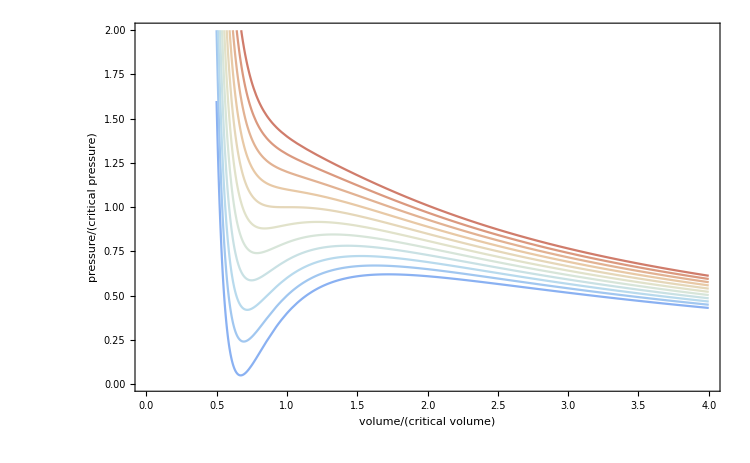

```mathematica
isothermPlot=With[ {curves = Table[pNormalvdWEquationOfStateNormalized[vNormalized,tNormalized],{tNormalized,0.85,1.1,0.025}]},
Plot[curves,{vNormalized,0.5,4}, ]
]
```

### Helmholtz Free Energy

The Helmholtz Free Energy for the Van der Waals gas can be derived from statistical mechanics

Where  is a constant that has units of [temperature^(3/2)/(volume)]  it depends  on Planck and Boltzmann constants.. The a and b come from equation of state for the van der Waals gas:

```mathematica
helmholtzFreeEnergy[a_,b_,r_,ϕ_][molarVolume_,temperature_]:=-8/3(r temperature (1+Log[(molarVolume-b)/ϕ temperature^(3/2)])+a/molarVolume);
```

We normalize the free energy by evaluating a and b at the critical values we obtained earlier

```mathematica
criticalSolutionsSubstitutions={a->(9 r tCritical vCritical)/8,b->vCritical/3}
```

{a→(9 r tCritical vCritical)/8,b→vCritical/3}

```mathematica
Clear[normalizedHelmholtzFreeEnergy]
```

And we divide by a characteristic energy to make the Helmholtz free energy dimensionless

```mathematica
normalizedHelmholtzFreeEnergy[V_,T_] = 
FullSimplify[helmholtzFreeEnergy[(9 boltzmansR tCritical vCritical)/8,vCritical/3,boltzmansR,tCritical^(3/2)vCritical][V vCritical,T tCritical]/(boltzmansR tCritical),Assumptions->tCritical> 0]
```

-(9+8 T V+8 T V Log[1/3 T^(3/2) (-1+3 V)])/(3 V)

```mathematica
normalizedHelmholtzFreeEnergy = Function[{vNormalized,tNormalized},
Evaluate[FullSimplify[helmholtzFreeEnergy[(9 boltzmansR tCritical vCritical)/8,vCritical/3,boltzmansR,tCritical^(3/2)vCritical][vNormalized vCritical,tNormalized tCritical]/(boltzmansR tCritical),Assumptions->tCritical> 0]]
]
```

Function[{vNormalized,tNormalized},-(9+8 tNormalized vNormalized+8 tNormalized vNormalized Log[1/3 tNormalized^(3/2) (-1+3 vNormalized)])/(3 vNormalized)]

```mathematica
With[{
simplifiedExpression=FullSimplify[helmholtzFreeEnergy[(9 boltzmansR tCritical vCritical)/8,vCritical/3,boltzmansR,tCritical^(3/2)vCritical][vNormalized vCritical,tNormalized tCritical]/(boltzmansR tCritical),Assumptions->tCritical> 0]},

normalizedHelmholtzFreeEnergy[vNormalized_,tNormalized_]:=simplifiedExpression
]
```

SetDelayed::write: Tag Function in Function[{vNormalized,tNormalized},-(9+8 tNormalized vNormalized+8 tNormalized vNormalized Log[1/3 tNormalized^(3/2) (-1+Times[«2»])])/(3 vNormalized)][vNormalized$_,tNormalized$_] is Protected.

$Failed

For example:

```mathematica
normalizedHelmholtzFreeEnergy[v,t]
```

-(9+8 t v+8 t v Log[1/3 t^(3/2) (-1+3 v)])/(3 v)

```mathematica
normalizedHelmholtzFreeEnergy[.6,.7]
```

-3.4007

And plot this for various normalized temperatures

```mathematica
normalizedHelmholtzFreeEnergy[vNormalized,0.75]
```

-(9+6. vNormalized+6. vNormalized Log[0.216506 (-1+3 vNormalized)])/(3 vNormalized)

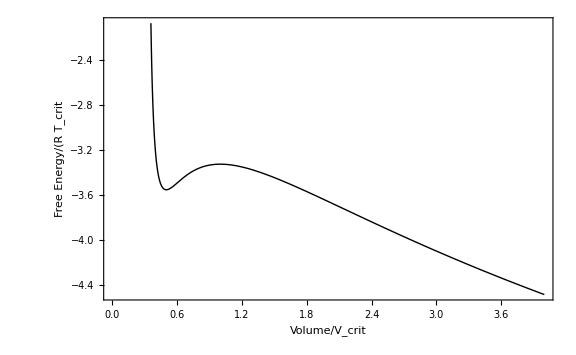

```mathematica
Plot[normalizedHelmholtzFreeEnergy[vNormalized,0.75],{vNormalized,0,4},Frame->True,BaseStyle->18,PlotStyle->{GrayLevel[0],Thickness[Large]},ImageSize->Large,FrameLabel->{"Volume/V_crit","Free Energy/(R T_crit"}]
```

```mathematica
Manipulate[Plot[normalizedHelmholtzFreeEnergy[vNormalized,temperature],{vNormalized,0,10},],{{temperature,0.75},0.5,1.25},Paneled->False]
```

The Helmholtz free energy develops a concavity for temperatures below the critical isotherm

Below the critical point, a common tangent can be constructed

That is, we seek to find a straight line which intersects our free energy at two points  and  and is tangent at our free energy at those points

Mathematically, this is specified by matching their derivatives according to:

```mathematica
Clear[commonTangentPoints,initialGuesses]

initialGuesses=<|0.75->{0.5,5}|>;
commonTangentPoints[temperature_?(0.75<= #<1&)]:=commonTangentPoints[temperature]=Module[{reversedGuesses,guessesV,guessesA,isotherm,sol},

reversedGuesses=AssociationMap[Reverse,initialGuesses];
guessesV=First[Nearest[reversedGuesses,temperature]];

isotherm[vNormalized_]=normalizedHelmholtzFreeEnergy[vNormalized,temperature];
guessesA=isotherm/@guessesV;

sol=Quiet@FindRoot[{
a1==isotherm[v1],
a2==isotherm[v2],
isotherm'[v1]==isotherm'[v2],
isotherm'[v1]==(a2-a1)/(v2-v1)
},
{v1,guessesV[[1]]},{v2,guessesV[[2]]},{a1,guessesA[[1]]},{a2,guessesA[[2]]}];

AssociateTo[initialGuesses,(temperature->{v1,v2})/.sol];

{
{{v1,a1},{v2,a2}}/.sol,
Piecewise[{{a1+isotherm'[v1] (vNormalized-v1),v2>vNormalized>v1}},_]/.sol
}]

commonTangentPoints[temperature_?(#>=1&)]:=With[{pts=commonTangentPoints[0.999999][[1,All,1]]},
{{#,normalizedHelmholtzFreeEnergy[#,temperature]}&/@pts,normalizedHelmholtzFreeEnergy[#,temperature]&}]
```

```mathematica
Manipulate[
With[{commonPts=commonTangentPoints[temperature]},
Show[Plot[{normalizedHelmholtzFreeEnergy[vNormalized,temperature],commonPts[[2]]},{vNormalized,0,5},],Graphics[{{PointSize[0.015],Red,Point[commonPts[[1]]]},{Dashed,Line[{{#[[1]],-10},{#[[1]],0}}]&/@commonPts[[1]]}}]]],{temperature,0.75,1.1},Paneled->False]
```

#### Gibbs Free Energy

Let’s use our Legendre transforms from above to define the Gibbs Free energy

First, remember the differential form of the Helmholtz Free energy

and use it to define the pressure at constant temperature and mole numbers

And then use our Legendre transform to define the Gibbs Free energy as

This allows us to express the GIbbs-free energy parametrically with the normalized volume as

```mathematica
parametricGibbs[vNormalized_,tNormalized_]=FullSimplify[{
-Derivative[1,0][normalizedHelmholtzFreeEnergy][vNormalized,tNormalized],normalizedHelmholtzFreeEnergy[vNormalized,tNormalized]-Derivative[1,0][normalizedHelmholtzFreeEnergy][vNormalized,tNormalized]vNormalized
}];

parametricGibbsFlipped[vNormalized_,tNormalized_]={-#2,#1}&@@parametricGibbs[vNormalized,tNormalized]
```

{6/vNormalized-(8 tNormalized)/(-3+9 vNormalized)+8/3 tNormalized Log[1/3 tNormalized^(3/2) (-1+3 vNormalized)],-3/vNormalized^2+(8 tNormalized)/(-1+3 vNormalized)}

We can now put everything together!

```mathematica
linkedVisualization[tNormalized_]:=Block[{
padding={{45,5},{45,5}},
colors={Red,RGBColor[0,1/3,0],Blue},
gibbs,helm,press
},

gibbs=ParametricPlot[parametricGibbsFlipped[vNormalized,tNormalized],{vNormalized,0,4},Frame->True,BaseStyle->14,PlotStyle->Directive[Thick,colors[[1]]],FrameLabel->{"Gibbs Free Energy","Pressure"},PlotRange->{Automatic,{0,2}},ImagePadding->padding,ImageSize->300,AspectRatio->1/2];

helm=Plot[normalizedHelmholtzFreeEnergy[vNormalized,tNormalized],{vNormalized,0,4},Frame->True,BaseStyle->14,PlotRange->{{0,4},Automatic},PlotStyle->Directive[Thick,colors[[2]]],FrameLabel->{"Volume","Free Energy"},ImagePadding->padding,ImageSize->300,AspectRatio->1/2];

press=Plot[pNormalvdWEquationOfStateNormalized[vNormalized,tNormalized],{vNormalized,0.5,4},Frame->True,PlotRange->{{0,4},{0,2}},BaseStyle->14,FrameLabel->{"Volume","Pressure"},ImagePadding->padding,ImageSize->300,PlotStyle->Directive[Thick,colors[[3]]],AspectRatio->1/2];

GraphicsGrid[{{"",helm},{gibbs,press}},ImageSize->750]

]
```

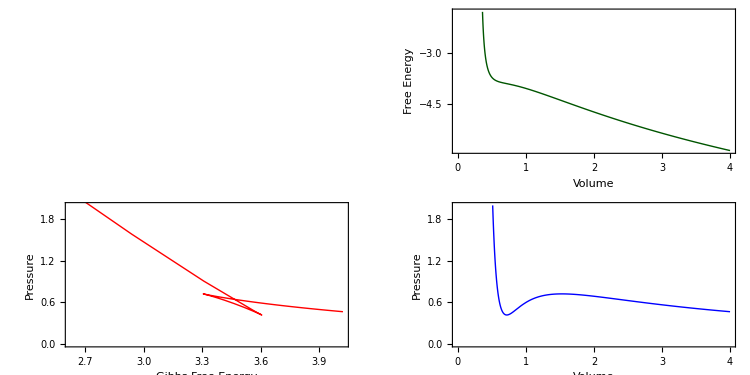

```mathematica
linkedVisualization[0.9]
```

```mathematica
Manipulate[linkedVisualization[temperature],{{temperature,1},0.85,1.1},Paneled->False]
```

Remember our condition for stability re: the isothermal bulk modulus from last lecture?

We can use the differential form of the Gibbs free energy to express the volume as:

This suggests our stability condition can be expressed in terms of the curvature of the Gibbs function:

Notice how there’s regions outside the equilibrium pressure (kink in Gibbs function), which nonetheless are thermodynamically stable

This is a common feature in many thermodynamic phenomena, which you will explore more in your second assignment

In particular, in your second assignment, you will explore yet another construction, called the Maxwell equal-area construction, to connect all these methods!